```mathematica
μ0 = 4π*10^-7;
```

```mathematica
(*Tesla*)
Bcoil[z_,zpos_,turns_, radius_, current_]:= (μ0*current*turns)/2 radius^2/((radius^2+(zpos-z)^2)^(3/2)) ;
(*Tesla/m*)
dBdzcoil[z_,zpos_,turns_, radius_, current_]:= (3*μ0*current*turns)/2 radius^2/((radius^2+(zpos-z)^2)^(5/2))(zpos-z);
```

```mathematica
(*MOT is at z=0*)
(*Plot gradient, but make sure you get units right: (something like  8-2.5z)*)
```

```mathematica
Manipulate[
Show[
Plot[{(Bcoil[z*10^-3,pos1*10^-3,1,rad1*10^-3,0]+Bcoil[z*10^-3,pos2*10^-3,1,rad2*10^-3,curr])*10^4,9-2.5/10 z},{z,-200,200},PlotRange->{{-20,20},{0,10}},AxesLabel->{"Position (mm)","B field (G)"}]],
{{pos1,-50},-100, -1 },{{pos2,50},1,100},{{rad1,120},1,140},{{rad2,120},1,140},{{curr,100},1,1000}]
```

## Two coil trial

```mathematica
totalField[z1_,z2_,turns1_,turns2_,rad1_,rad2_]:=-Bcoil[z1,turns1, rad1]+Bcoil[z2,turns2, rad2];
totalGrad[z1_,z2_,turns1_,turns2_,rad1_,rad2_]:=-dBdzcoil[z1,turns1, rad1]+dBdzcoil[z2,turns2, rad2];
z1fix=-9 cm; z2fix=14 cm; rad2fix=6 cm;

ContourPlot3D[{
totalField[z1fix,z2fix,u,v,w cm,rad2fix]== 8 gauss,
totalGrad[z1fix,z2fix,u,v,w cm,rad2fix] gaussPercm ==-7 },
{u,1,10},{v,1,10},{w,3,10},AxesLabel->{"zPos","Turns","Rad"}]
```

-Graphics3D-

```mathematica
Manipulate[
Show[
Plot[totalField[(a-z) cm,(b-z) cm,c,d,e cm,f cm]/gauss,{z,-15,15},PlotRange->{-15,15}],Plot[-6+0.7x,{x,-2,2},PlotStyle->{Red,Dashed}],ParametricPlot[{-12.5,y},{y,-20,20},PlotStyle->{Dashed,Black}]],{a,-20,-5},{b,10,20},{c,0,10},{d,0,10},{e,3,10},{f,3,10}
]
```

```mathematica
1.4 2.54
```

3.556

```mathematica
ContourPlot3D[
dBdzcoil[u cm,v,w cm] gaussPercm ==0.5 ,
{u,1,15},{v,1,10},{w,1,8},AxesLabel->{"zPos","Turns","Rad"}]
```

-Graphics3D-

```mathematica
dBdzcoil[8 cm,1,4 cm] gaussPercm//N
```

0.547936

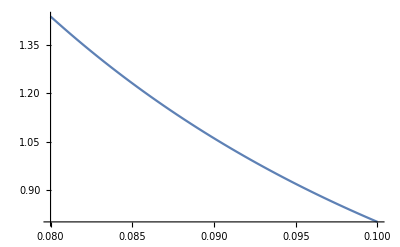

```mathematica
Plot[(Bcoil[z, 0, 130, 0.034])*10^4,{z,0.08,.1}]
```